# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 13 - Applications of the Ising Model

Reminder:  This assumes that you have defined the functions from Chapter 12

## 13.2 PHASE TRANSITIONS

### 13.2.1 Model

```mathematica
J=-1;B=0;(*ferromagnetic,no external magnetic field*)
config=checkerboardConfig;(*6 x 6 checkerboard lattice*)
EvsT={}; CvsT={}; MvsT={}; (*empty lists to store E,Cv,M*)

Do[
results=runMC[kT,J,B,10^4,2*10^5,10^3,config,MCstepPBC,energyIsing2DPBC];

AppendTo[EvsT,{kT,results[[1]]}];AppendTo[CvsT,{kT,results[[2]]}];AppendTo[MvsT,{kT,results[[3]]}];
config=results[[4]];
,{kT,4,1,-0.1}
];
```

### 13.2.2 Results

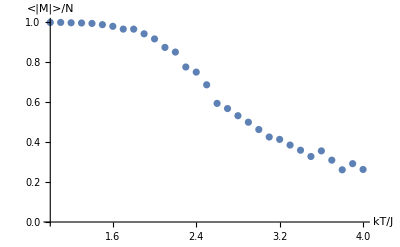

```mathematica
ListPlot[ MvsT,
AxesLabel->{"kT/J","<|M|>/N"},AxesOrigin->{1,0}]
```

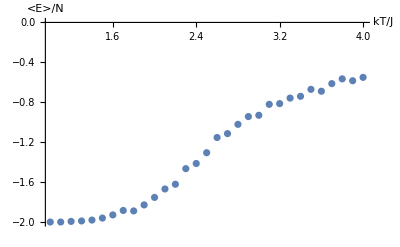

```mathematica
ListPlot[ EvsT,AxesLabel->{"kT/J","<E>/N"}]
```

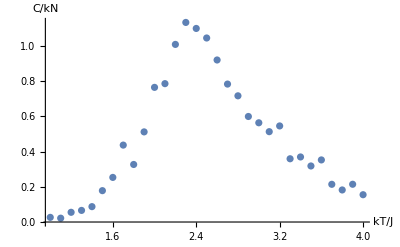

```mathematica
ListPlot[ CvsT,AxesLabel->{"kT/J","C/kN"}]
```

## 13.3 SOLUBILITY AND MISCIBILITY

### 13.3.1 Model

```mathematica
countTotallySolvated[config_,soluteType_]:=Module[
{totalSolvated=0,nnSameType},
Do[
nnSameType=0;If[config[[row,col]]==soluteType,If[(row>1)&&(config[[row-1,col]]==soluteType),nnSameType++];If[(row<Length[config])&&(config[[row+1,col]]==soluteType),
nnSameType++];
If[(col>1)&&(config[[row,col-1]]==soluteType),nnSameType++];If[(col<Length[config])&&(config[[row,col+1]]==soluteType),
nnSameType++];

If[nnSameType==0,totalSolvated++];
];
,{row,1,Length[config]},{col,1,Length[config]}
];
totalSolvated
];
```

```mathematica
runMCv2[kT_,J_,B_,nEquil_,nDataCol_,sampleInterval_,config_,MCstepFunction_,energyFunction_]:=Module[
{Esamples={},Msamples={},
(*new*)NsolvSamples={},newConfig=config},Do[newConfig=MCstepFunction[kT,J,B,newConfig],{nEquil}];
Do[
newConfig=MCstepFunction[kT,J,B,newConfig];If[Mod[i,sampleInterval]==0,
AppendTo[Esamples,energyFunction[newConfig,J,B]];AppendTo[Msamples,Abs[netMagnetizationPerSpin[newConfig]]];(*new*)AppendTo[NsolvSamples,countTotallySolvated[newConfig,-1]];
];
,{i,1,nDataCol}];
(*return the following data:*){Mean[Esamples]/(Length[config]^2),(*energy per spin*)Variance[Esamples]/(Length[config]^2*kT^2),(*heat capacity*)
Mean[Msamples],(*net magnetization per spin*)
(*new*)Mean[NsolvSamples],(*number of totally solvated-1 sites*)newConfig (*the final configuration*)}
];
```

### 13.3.2 Advanced Mathematica techniques: Timing[] is everything

```mathematica
J=-1;B=0;kT=4;
config=ConstantArray[+1,{10,10}]; (*create a 10 x 10 array of spins*)
config[[5,;;]]=-1; (*create a stripe down the middle*)

Timing[
runMCv2[kT,J,B,10000,200000,1000,config,MCstepConstN,energyIsing2D] ]
```

{107.489,{-12413/10000,509631/15920000,4/5,483/100,{{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,-1,1,1,1,1,1},{-1,1,1,1,1,1,1,1,1,1},{1,1,-1,1,1,-1,1,1,1,1},{1,1,1,1,1,1,1,1,1,-1},{-1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,-1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,-1,-1,1,1,1,1,1,1},{1,1,1,1,1,1,-1,1,1,1}}}}

```mathematica
localEnergyIsing2D[config_,J_,B_,row_,col_]:=Module[
{energyB=0,energyJ=0},
energyB+=B*config[[row,col]];
If[row>1,(*up*)
energyJ+=J*config[[row-1,col]]*config[[row,col]] ];If[row<Length[config],(*down*)energyJ+=J*config[[row+1,col]]*config[[row,col]] ];If[col>1,(*left*)
energyJ+=J*config[[row,col-1]]*config[[row,col]] ];
If[col<Length[config],(*right*)energyJ+=J*config[[row,col+1]]*config[[row,col]] ];energyB+energyJ (*note:no double counting to remove*)
];
```

```mathematica
MCstepConstNv2[kT_,J_,B_,config_]:=Module[
{newConfig=config,rowA,colA,rowB,colB,spinA,spinB,Estart,Eend,configDidChange=False},{rowA,colA,rowB,colB}=RandomInteger[{1,Length[config]},4];

spinA=config[[rowA,colA]];(*spin values at each position*)
spinB=config[[rowB,colB]];

If[spinA!=spinB,(*only do MC procedure if something changed*)newConfig[[rowA,colA]]=spinB; (*first,interchange the spins*)
newConfig[[rowB,colB]]=spinA;

(*revised:replace former Estart and Eend evaluation*)
If[(rowA-rowB)^2+(colA-colB)^2<5,(*are spins nearby?*)(*true:too close to separate the evaluations*)Estart=energyIsing2D[config,J,B];Eend=energyIsing2D[newConfig,J,B];
,
(*false:far enough apart to make two separate evaluations*)Estart=localEnergyIsing2D[config,J,B,rowA,colA]+localEnergyIsing2D[config,J,B,rowB,colB];Eend=localEnergyIsing2D[newConfig,J,B,rowA,colA]+localEnergyIsing2D[newConfig,J,B,rowB,colB];
];

(*MC accept/reject is the same as before*)
If[Eend<Estart,(*did the energy decrease?*)
configDidChange=True;,(*energy decreased,accept new config.*)If[RandomReal[]≤Exp[-(Eend-Estart)/kT],(*else,try MC swap*)configDidChange=True;
];
];
];If[configDidChange,(*did configuration change during this process?*)newConfig,(*configDidChange==True,so return the new spin config.*)
config] (*otherwise return the original spin configuration*)
];
```

```mathematica
Timing[
runMCv2[kT,J,B,10^4,2*10^5,10^3,config,MCstepConstNv2,energyIsing2D]
]
```

{23.1334,{-12403/10000,527791/15920000,4/5,971/200,{{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,-1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{-1,1,1,1,1,1,1,1,1,1},{-1,1,-1,1,1,1,1,1,1,1},{-1,1,1,1,1,-1,-1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,-1,1,1,1,1},{-1,-1,1,1,1,1,1,1,1,1}}}}

```mathematica
energyIsing2D[config_,J_,B_]:=Module[
{energyB=0,energyJ=0},
Do[ (*loop over rows and columns*)
energyB+=B*config[[row,col]];
If[row>1,(*up*)
energyJ+=J*config[[row-1,col]]*config[[row,col]] ];If[row<Length[config],(*down*)energyJ+=J*config[[row+1,col]]*config[[row,col]] ];If[col>1,(*left*)
energyJ+=J*config[[row,col-1]]*config[[row,col]]];(*revised-->*)If[col<Length[config[[1]]],(*right*)energyJ+=J*config[[row,col+1]]*config[[row,col]]];
,{row,1,Length[config]},(*revised-->*){col,1,Length[config[[1]]]}
];
energyB+(energyJ/2) (*remove double counting*)
];
```

```mathematica
MCstepConstNv3[kT_,J_,B_,config_]:=Module[
{newConfig=config,rowA,colA,rowB,colB,spinA,spinB,Estart,Eend,configDidChange=False,(*new*)minRow,maxRow,minCol,maxCol},{rowA,colA,rowB,colB}=RandomInteger[{1,Length[config]},4];spinA=config[[rowA,colA]]; (*spin values at each position*)
spinB=config[[rowB,colB]];
If[spinA!=spinB,(*only do MC procedure if something changed*)newConfig[[rowA,colA]]=spinB; (*first,interchange the spins*)
newConfig[[rowB,colB]]=spinA;

(*replace former Estart and Eend evaluation*)If[(rowA-rowB)^2+(colA-colB)^2<5,(*are spins nearby?*)(*true:too close to separate the evaluations*)
(*begin revision*)
minRow=Max[Min[rowA,rowB]-1,1];maxRow=Min[Max[rowA,rowB]+1,Length[config]];minCol=Max[Min[colA,colB]-1,1];maxCol=Min[Max[colA,colB]+1,Length[config[[1]]]];Estart=energyIsing2D[config[[minRow;;maxRow,minCol;;maxCol]],J,B];
Eend=energyIsing2D[newConfig[[minRow;;maxRow,minCol;;maxCol]],J,B];(*end revision*)
,
(*false:far enough apart to make two separate evaluations*)Estart=localEnergyIsing2D[config,J,B,rowA,colA]+localEnergyIsing2D[config,J,B,rowB,colB];Eend=localEnergyIsing2D[newConfig,J,B,rowA,colA]+localEnergyIsing2D[newConfig,J,B,rowB,colB];
];

(*MC accept/reject is the same as before*)If[Eend<Estart,(*did the energy decrease?*)
configDidChange=True;,(*if energy decreased,accept new config.*)If[RandomReal[]≤Exp[-(Eend-Estart)/kT],(*else,try MC swap*)configDidChange=True;
];
];
];If[configDidChange,(*did configuration change during this process?*)newConfig,(*configDidChange==True,so return new spin configuration*)
config] (*otherwise return the original spin configuration*)
];
```

```mathematica
Timing[
runMCv2[kT,J,B,10^4,2*10^5,10^3,config,MCstepConstNv3,energyIsing2D];
]
```

{18.4486,Null}

### 13.3.3 Results

```mathematica
J=-1;B=0;
config=ConstantArray[+1,{10,10}];(*create a 10 x 10 array of spins*)
config[[5,;;]]=-1;(*make a stripe down the middle*)
EvsT={}; CvsT={}; MvsT={}; SolvvsT={};
Do[
results=runMCv2[kT,J,B,10000,200000,1000,config,MCstepConstNv3,energyIsing2D];

AppendTo[EvsT,{kT,results[[1]]}];AppendTo[CvsT,{kT,results[[2]]}];AppendTo[MvsT,{kT,results[[3]]}];AppendTo[SolvvsT,{kT,results[[4]]/10}];(*fraction solvated*)
config=results[[5]];
,{kT,4,10^-6,-0.1}
];
```

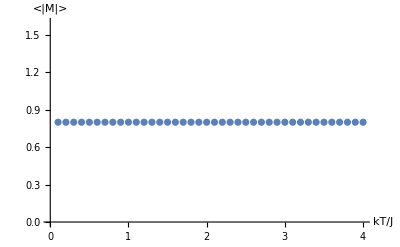

```mathematica
ListPlot[ MvsT,AxesLabel->{"kT/J","<|M|>"}]
```

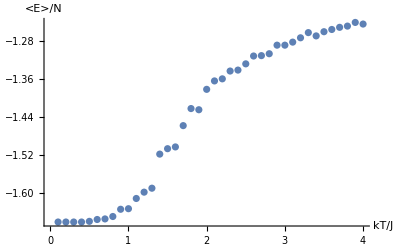

```mathematica
ListPlot[ EvsT,AxesLabel->{"kT/J","<E>/N"}]
```

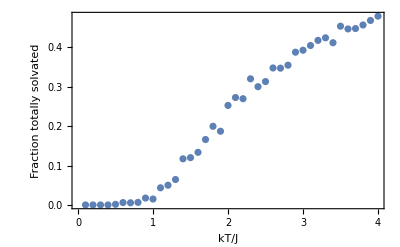

```mathematica
ListPlot[ SolvvsT,Frame->{True,True,False,False},FrameLabel->{"kT/J","Fraction totally solvated"} ]
```

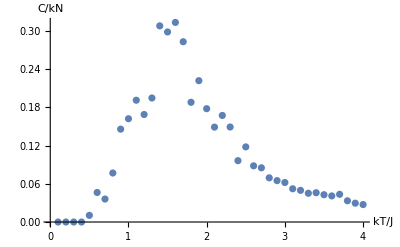

```mathematica
ListPlot[ CvsT,AxesLabel->{"kT/J","C/kN"}]
```

## 13.4 GAS ADSORPTION ISOTHERMS

### 13.4.2 Widom insertion method

```mathematica
insertionAverage[kT_,Eint_,Eads_,config_,nTrials_]:=Module[
{sum=0,row,col,newConfig},
Do[ (*loop over trials*)
{row,col}=RandomInteger[{1,Length[config]},2];If[config[[row,col]]==0,(*can only add particle to unoccupied site*)newConfig=config;
newConfig[[row,col]]=1;sum+=Exp[-localEnergyIsing2D[newConfig,Eint,Eads,row,col]/kT];
];
,{nTrials}];
(sum/nTrials) (*return insertion average,B*)
];
```

```mathematica
runWidomInsertion[kT_,Eint_,Eads_,nEquil_,nSwap_,nInsertionTrials_,nRepeats_,config_,MCstepFunction_,insertionFunction_]:=Module[
{newConfig=config,sum=0},
(*first equilibrate*)
Do[newConfig=MCstepFunction[kT,Eint,Eads,newConfig];,{nEquil}];(*then run insertion trials*)
Do[
Do[newConfig=MCstepFunction[kT,Eint,Eads,newConfig];,{nSwap}];
sum+=insertionFunction[kT,Eint,Eads,newConfig,nInsertionTrials];
,{nRepeats}];
(sum/nRepeats) (*return average over MC configurations*)
];
```

### 13.4.3 Results

```mathematica
generateConfig[occupancy_,length_]:=Table[ If[(i-1)*length+j≤occupancy*length^2,1,0]
,{i,1,length},{j,1,length}]
```

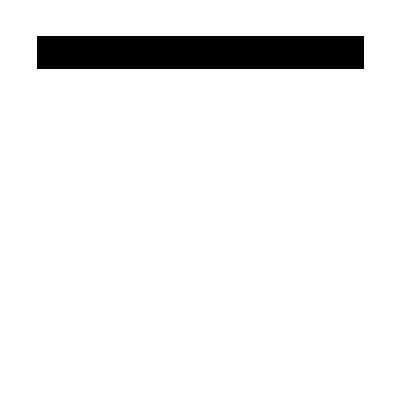
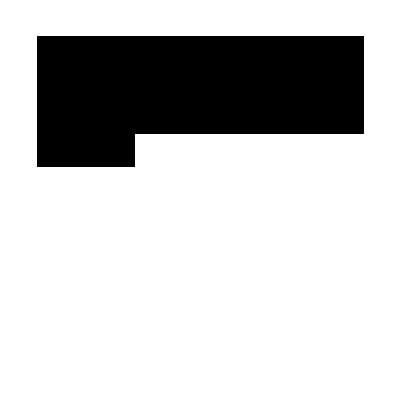
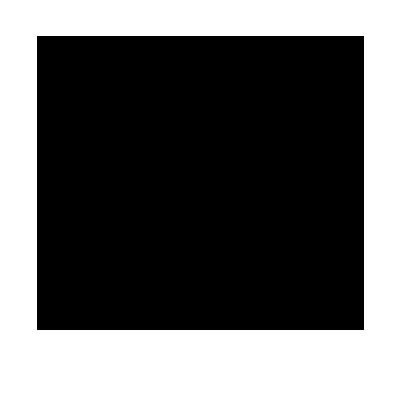

```mathematica
{ArrayPlot[generateConfig[0.1,10]],
ArrayPlot[generateConfig[0.33,10]],
ArrayPlot[generateConfig[0.9,10]]}
```

```mathematica
kT=0.5;adsorptionEnergy=-1;interactionEnergy=0;
data={};boxLength=10;

Do[(*loop over occupancy fraction*)
config=generateConfig[occupancy,boxLength];AppendTo[data,{occupancy/runWidomInsertion[kT,interactionEnergy,adsorptionEnergy,10000,1000,200,200,config,MCstepConstNv3,insertionAverage],
occupancy}
];
,{occupancy,0.01,0.91,0.1}];
```

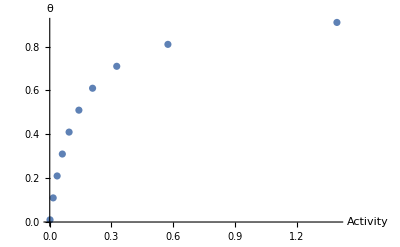

```mathematica
g1=ListPlot[ data,
PlotRange->All,AxesLabel->{"Activity","θ"} ]
```

```mathematica
langmuirIsotherm=K*P/(1+K*P);
fit1=FindFit[data,langmuirIsotherm,{{K,0}},P]
```

{K→7.41085}

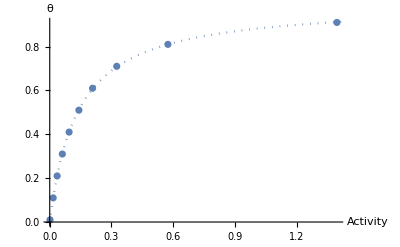

```mathematica
Show[ g1,Plot[langmuirIsotherm/.fit1,{P,0,10},
PlotStyle->Dotted,PlotRange->All] ]
```